```mathematica
Length/@{{1,2},{1,2,3,4}}
```

{2,4}

```mathematica
sentmt=Classify["Sentiment",TextCases[WikipediaData["open source"],"Noun"]];
list=
PieChart[Table[Count[sentmt,a],{a,DeleteDuplicates[sentmt]}],ChartLabels->DeleteDuplicates[sentmt]]
```

-Graphics-

```mathematica
li=TextCases[WikipediaData["modernity"],"Noun"];
sentmt=Classify["Sentiment",li];
list=DeleteDuplicates[sentmt]
PieChart[Table[Count[sentmt,a],{a,list}],ChartLabels->list]
```

{Positive,Negative,Neutral,Indeterminate}

-Graphics-

```mathematica
sentmt=Classify["Sentiment",TextCases[WikipediaData["technology"],"Noun"]];
list=DeleteDuplicates[sentmt]
PieChart[Table[Count[sentmt,a],{a,list}],ChartLabels->list]
```

{Positive,Neutral,Indeterminate,Negative}

-Graphics-

```mathematica
EntityClass["Country","GroupOf5"]//EntityProperties
```

```mathematica
GeoGraphics/@EntityList[EntityClass["Country","GroupOf5"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Binarize/@EntityClass["Country","Europe"]["Flag"]//ImageCollage
```

-Graphics-

```mathematica
Characters["Wolfram"]
```

{W,o,l,f,r,a,m}

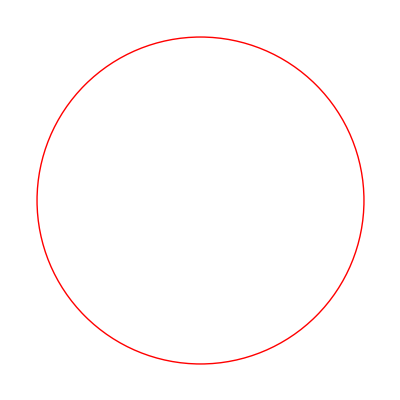
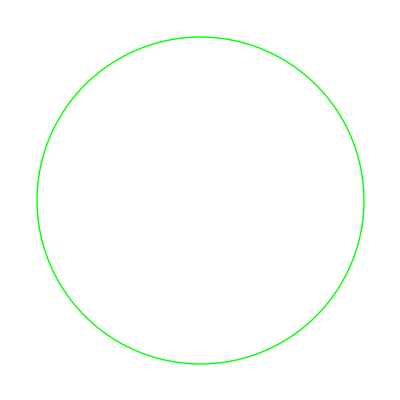
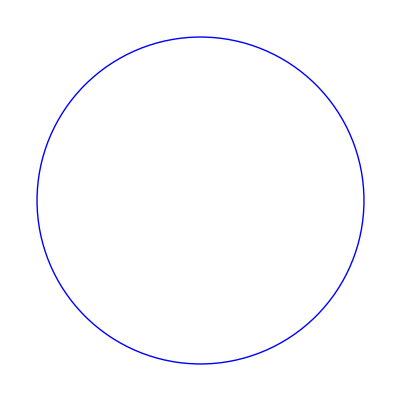

```mathematica
Graphics/@{Style[Circle[],Red,Thick],Style[Circle[],Green,Thick],Style[Circle[],Blue,Thick]}
```

```mathematica
Blur/@{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Blur[#,10]&/@{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityClass["Planet",All]/@{"Image","Mass"}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{3.3×10^23 kg,4.867×10^24 kg,5.97×10^24 kg,6.417×10^23 kg,1.898×10^27 kg,5.683×10^26 kg,8.681×10^25 kg,1.024×10^26 kg}}

```mathematica
Framed/@(Column[{ToUpperCase[#],#}]&/@Alphabet[])
```

{A
a,B
b,C
c,D
d,E
e,F
f,G
g,H
h,I
i,J
j,K
k,L
l,M
m,N
n,O
o,P
p,Q
q,R
r,S
s,T
t,U
u,V
v,W
w,X
x,Y
y,Z
z}

```mathematica
Framed[#,Background->RandomColor[]]&/@(Style[#,RandomColor[]]&/@Alphabet[])
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
Framed[Style[#,RandomColor[]],Background->RandomColor[]]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}







```mathematica
EntityClass["Country","GroupOf5"]["Flag"]
```

```mathematica
Grid[{#,#["Flag"]}&/@EntityList[EntityClass["Country","GroupOf5"]],Frame->All]
```

France | -Graphics-
Germany | -Graphics-
Japan | -Graphics-
United Kingdom | -Graphics-
United States | -Graphics-

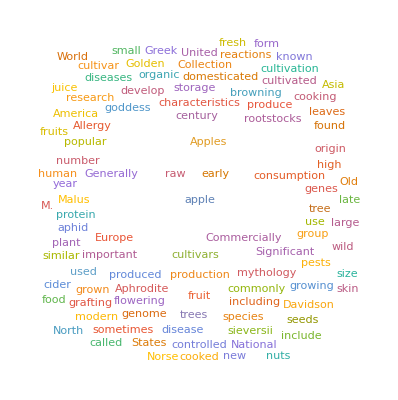
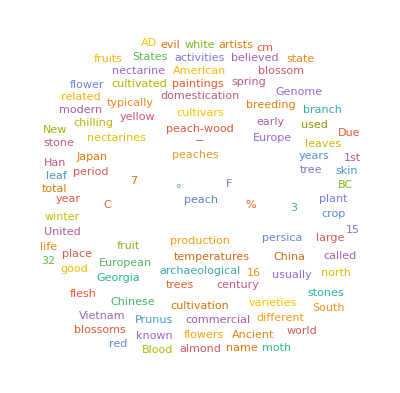
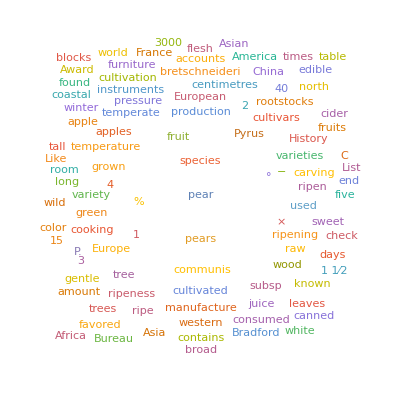

```mathematica
WordCloud/@(WikipediaData[#]&/@{"apple","peach","pear"})
```

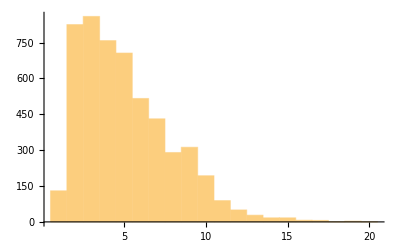
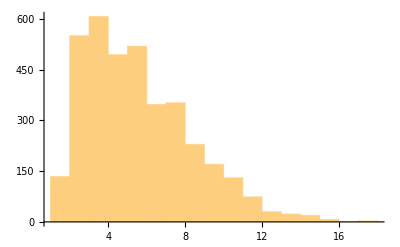
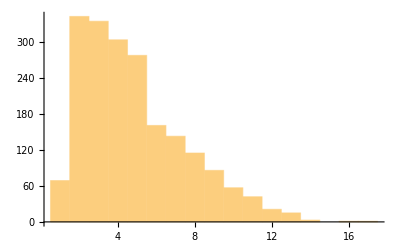

```mathematica
Histogram@StringLength@TextWords@WikipediaData[#]&/@{"apple","peach","pear"}
```

```mathematica
LinguisticAssistant
```

Failure[…]

```mathematica
(#^2+1&)/@Range[10]
```

{2,5,10,17,26,37,50,65,82,101}

```mathematica
Range[10]^2+1
```

{2,5,10,17,26,37,50,65,82,101}

```mathematica
NestList[ColorNegate[EdgeDetect[#]] &, -Graphics-, 6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
f[#]&[1]
```

f[1]

```mathematica
NestList[Blend[{#,White}]&,Red,20]
```

{RGBColor[1, 0, 0],RGBColor[1, Rational[1, 2], Rational[1, 2]],RGBColor[1, Rational[3, 4], Rational[3, 4]],RGBColor[1, Rational[7, 8], Rational[7, 8]],RGBColor[1, Rational[15, 16], Rational[15, 16]],RGBColor[1, Rational[31, 32], Rational[31, 32]],RGBColor[1, Rational[63, 64], Rational[63, 64]],RGBColor[1, Rational[127, 128], Rational[127, 128]],RGBColor[1, Rational[255, 256], Rational[255, 256]],RGBColor[1, Rational[511, 512], Rational[511, 512]],RGBColor[1, Rational[1023, 1024], Rational[1023, 1024]],RGBColor[1, Rational[2047, 2048], Rational[2047, 2048]],RGBColor[1, Rational[4095, 4096], Rational[4095, 4096]],RGBColor[1, Rational[8191, 8192], Rational[8191, 8192]],RGBColor[1, Rational[16383, 16384], Rational[16383, 16384]],RGBColor[1, Rational[32767, 32768], Rational[32767, 32768]],RGBColor[1, Rational[65535, 65536], Rational[65535, 65536]],RGBColor[1, Rational[131071, 131072], Rational[131071, 131072]],RGBColor[1, Rational[262143, 262144], Rational[262143, 262144]],RGBColor[1, Rational[524287, 524288], Rational[524287, 524288]],RGBColor[1, Rational[1048575, 1048576], Rational[1048575, 1048576]]}

GoldenRation

```mathematica
NestList[Sqrt[1+#]&,1,15]//N
```

{1.,1.41421,1.55377,1.59805,1.61185,1.61612,1.61744,1.61785,1.61798,1.61802,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803}

```mathematica
Join[{0},{1,1}]+Join[{1,1},{0}]
```

{1,2,1}

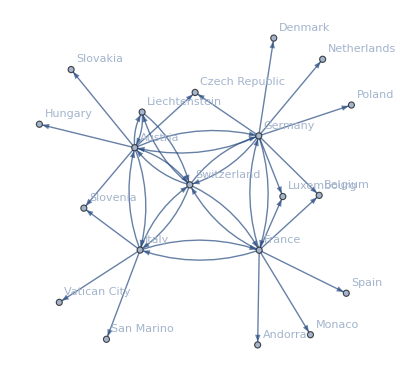

```mathematica
NestGraph[#["BorderingCountries"]&,Entity["Country","Switzerland"],2,VertexLabels->All]
```

```mathematica
NestList[Blur,Rasterize[Style[X,30]],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList[Rotate[Framed[#],RandomReal[]]&,Style[A,50],5]
```

{A,A,A,A,A,A}

```mathematica
CloudDeploy[Manipulate[Graphics[Table[Circle[{0,0},r],{r,min,max}]],{min,1,30,1},{max,1,30,1}]]
```

CloudObject::srverr: Cloud server is not able to complete a request.

$Failed